# Artillery Aim Simulator

## Collin Davis and Chandler Jensen

## General Information:

I believe the easiest way to go about this project is to pick an artillery weapon currently in use by the United States military and use it for our simulation. Perhaps if we were to continue the project beyond the class we could add different weapons and allow the user to pick, but let’s not get ahead of ourselves.

Wikipedia has some good info on different artillery weapons, I think the M777 Howitzer is a good choice, coupled with the 155mm M795 shell. It has the following specifications (according to Wikipedia):
Range of Elevation: 0° - +71.7°
Muzzle Velocity: 827 m/s
Effective Firing Range: 22.5km

## Global Variables:

```mathematica
V0=827; (* V0 is the initial velocity of the shell *)
maxRange=22500; (* maximum range of the cannon *)
elevationMin=0Degree; (* minimum angle between horizontal plane and cannon *)
elevationMax=71.7Degree; (* maximum angle between horizontal plane and cannon *)
ag=-9.8;(*this is the accelotration of gravity*)
```

## Artillery Simulation

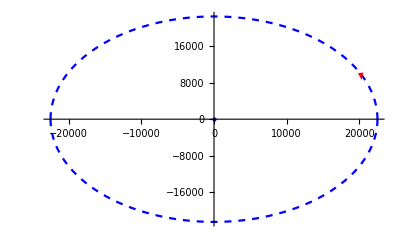

Target Position is:

{20305.2,8618.11}

Target Speed is:

18.6784 m/s

{22.9977,9.21284}

```mathematica
(* Target Location Generation *)
rangePlot=Plot[{y=Sqrt[maxRange^2-x^2],y=-Sqrt[maxRange^2-x^2]},{x,-maxRange,maxRange},PlotRange->All,PlotStyle->{{Blue,Dashed},{Blue,Dashed}}];
targetPosition={RandomReal[{-maxRange,maxRange}],RandomReal[{-maxRange,maxRange}]} ;
While[targetPosition[[1]]^2+targetPosition[[2]]^2>maxRange^2,targetPosition={RandomReal[{-maxRange,maxRange}],RandomReal[{-maxRange,maxRange}]}]
targetX=targetPosition[[1]];
targetY=targetPosition[[2]];
artilleryPosition={0,0};
artilleryPoint=Graphics[{Blue,PointSize[Large],Point[{0,0}]}];

(* Target Movement Generation *)
targetSpeed=RandomReal[{0,35}]; (* I put 35 m/s as max speed as that is nearly 80 mph *)
targetDirection=RandomReal[{0,2π}];
targetVector=AngleVector[{targetSpeed,targetDirection}];
targetArrow=Graphics[{Arrowheads[0.05],Red,Arrow[{targetPosition,targetPosition+targetVector}]}];

(* Conditions Plot and Output *)
Show[rangePlot,targetArrow,artilleryPoint]
"Target Position is:"
targetPosition
"Target Speed is:"
targetSpeed "m/s"

(* Aiming *)
AutoAim[{xposition_,yposition_}]:=Module[{direction,angle,dxy,dx=xposition,dy=yposition,az=ag,v0=V0},dxy=√(dx^2+dy^2)(*the distance to the point*);
If[0<=dy/dxy ,If[0<=dx/dxy,direction=(ArcTan[dy/dx]180)/π,direction=(ArcTan[dy/dx]180)/π+180],If[0<=dx/dxy,direction=(ArcTan[dy/dx]180)/π+360,direction=(ArcTan[dy/dx]180)/π+180]]
;(*the direction that we will shoot in degrees*)
angle=(ArcSin[-(dxy az)/v0^2]180)/(2π);AimAngle={direction,angle}](*this is the Angle at which it shoots in degrees*)
(*this is the direction and angle if there is no air resistance or wind in the form {direction in degrees,angle in degrees}*)
AutoAim[targetPosition]
```

### Final 3D Plot

```mathematica
targetPos3D={targetPosition[[1]],targetPosition[[2]],1};
targetVec3D={targetVector[[1]],targetVector[[2]],0};
field=Plot3D[x-y=0,{x,-maxRange,maxRange},{y,-maxRange,maxRange},PlotRange->{0,10},PlotStyle->GrayLevel[0.9,0.73]];
targetPoint3D=Graphics3D[Arrow[{targetPos3D,targetPos3D+targetVec3D}]];
Show[field,targetPoint3D]
```

Set::write: Tag Plus in -22496.8+22496.8 is Protected.

-Graphics3D-